```mathematica
Quit
```

```mathematica
(* GA theory *)
```

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly,Exp};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={0,2};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]]x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomInteger[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
(*
Sqrt[1+x funcGA[x,#,grammar]^2];
(1+x func[x,#,grammar]^2);
*)
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=Sqrt[1+x func[x,#,grammar]^2]&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2[pigs[[j]],data],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
Speak["The end"];];
bestfitperstep]
```

```mathematica
(* end *)
```

```mathematica
(* Cosmo Theory and Data *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
FileNames["..\\data\\mock_*LC*"]
```

{..\data\mock_Eg_LCDM.txt,..\data\mock_fs8_LCDM.txt,..\data\mock_H_LCDM.txt}

```mathematica
data=Import["..\\data\\mock_H_LCDM.txt","Table"];
zmax=data[[All,1]]//Max;
```

```mathematica
(* Various params *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
Neff=3.046;
KtoeV=8.621738*10^-5;
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
f[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
```

```mathematica
(* H(z) and χ^2 for the CPL model *) 
ρcr[h_]:=8.098*10^-11 h^2 eV^4;
Ωγ[h_]:=Pi^2/30 gγ T^4/ρcr[h]/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV;
Ων[h_,Neff_]:=Neff*7/8(4/11)^(4/3)Ωγ[h]
aeq[om_?NumberQ,h_?NumberQ]:=(Ωγ[h]+Ων[h,Neff])/om;
H[a_,om_,w0_,wa_,n_,h_]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,n]]
chi2Hzwcdm[om_,w0_,wa_,n_,h_]:=Sum[((data[[i,2]]-H[1/(1+data[[i,1]]),om,w0,wa,n,h])/data[[i,3]])^2,{i,1,Length[data]}];
```

```mathematica
(* χ^2 for GA *)
chi20[f_,dat_]:=Module[{temp,ft},ft=(f/.x->#)&;temp=Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]])^2,{ii,1,Length[dat]}];
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
chi2[f_,dat_]:=Module[{temp,A,B,Γ,ft},ft=(f/.x->#)&;
A=Sum[(dat[[ii,2]]/dat[[ii,3]])^2,{ii,1,Length[dat]}];
B=Sum[((dat[[ii,2]]*ft[dat[[ii,1]]])/dat[[ii,3]]^2),{ii,1,Length[dat]}];
Γ=Sum[(ft[dat[[ii,1]]]/dat[[ii,3]])^2,{ii,1,Length[dat]}];
temp=A-B^2/Γ+0Log[Γ/(2π)];
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

```mathematica
H0marg[f_,dat_]:=Module[{temp,B,Γ,ft},ft=(f/.x->#)&;
B=Sum[((dat[[ii,2]]*ft[dat[[ii,1]]])/dat[[ii,3]]^2),{ii,1,Length[dat]}];
Γ=Sum[(ft[dat[[ii,1]]]/dat[[ii,3]])^2,{ii,1,Length[dat]}];;
temp=B/Γ;
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

```mathematica
H0marg[H[1/(1+x),0.305,-1,0,1,0.7]/H[1,0.305,-1,0,1,0.7],data]
```

69.3586

```mathematica
(* Best fit // normal case *)
fmin=FindMinimum[chi2Hzwcdm[om,-1,0,1,h],{om,0.3},{h,.67}]
Print["χ^2= ",fmin[[1]]]
Print["Number of points = ",Length[data]]
```

{15.3944,{om→0.304765,h→0.693743}}

χ^2= 15.3944

Number of points = 20

```mathematica
(* end *)
```

```mathematica
(* GA fit *)
```

```mathematica
LaunchKernels[7];
```

```mathematica
(*
generations=200;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
GApop=GAevo[1234,generations,100,0.75,0.25,True];
*)
```

```mathematica
generations=200;
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj]=GAevo[1234jj,generations,100,0.75,0.30,False];prog`pop++;prog`int=0;,{jj,1,samples}];
```

```mathematica
fmin
```

{15.3995,{om→0.305032,h→0.693702}}

```mathematica
chi2minGA=Table[{jj,GApop[jj][[-1,1]]},{jj,1,samples}]
```

{{1,-18.7646},{2,-14.8165},{3,-14.6278},{4,-35.9276},{5,-14.7932},{6,-41.8994},{7,-16.3719},{8,-14.8708},{9,-16.8969},{10,-31.7253}}

```mathematica
SortBy[chi2minGA,Last]//Reverse
```

{{3,-14.6278},{5,-14.7932},{2,-14.8165},{8,-14.8708},{7,-16.3719},{9,-16.8969},{1,-18.7646},{10,-31.7253},{4,-35.9276},{6,-41.8994}}

```mathematica
Rasterize[ListLogLogPlot[Table[GApop[jj][[All,1]]//Abs,{jj,1,samples}],Joined->True,PlotRange->{5,5000},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,fmin[[1]]},{generations,fmin[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14],ImageSize->300,RasterSize->1000]
```

-Graphics-

```mathematica
ffname="LCDM_mock_sample_02";
Export[ffname<>".zip",{ffname<>".m"->Table[GApop[jj],{jj,1,samples}]}]
```

LCDM_mock_sample_02.zip

```mathematica
GApop[3][[-1,2]]
```

√(1+x (-0.901334-0.575324 x+0.0204083 x^2-0.0000675109 x^7)^2)

```mathematica
HgaoH0[x_]:=√(1+x (-0.9013344555444585-0.5753244381634155 x+0.02040826183394463 x^2-0.00006751090930245668 x^7)^2)
```

```mathematica
chi2[H[1/(1+x),om,-1,0,1,h]/H[1,om,-1,0,1,h]/.fmin[[2]],data]
chi2[HgaoH0[x],data]
```

15.3944

14.6278

```mathematica
H0GA=H0marg[HgaoH0[x],data]
```

69.6519

```mathematica
HGA[z_]:=H0GA HgaoH0[z];
```

```mathematica
dH[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 data[[i,3]])(H0GA dH[data[[i,1]],a1,a2,a3,a4]+HGA[data[[i,1]]]-data[[i,2]])]+Erf[1/(√2 data[[i,3]])(H0GA dH[data[[i,1]],a1,a2,a3,a4]-HGA[data[[i,1]]]+data[[i,2]])]),{i,1,Length[data]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[data]}]]
```

```mathematica
chi2ga[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=chi2[HGA[x]+H0GA dH[x,a1,a2,a3,a4],data]
```

```mathematica
chi2tot[a1_,a2_,a3_,a4_]:=chi2CI[a1,a2,a3,a4]+chi2ga[a1,a2,a3,a4]
```

```mathematica
fminerrHtot2=FindMinimum[chi2tot[a1,a2,0,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
fminerrHtot3=FindMinimum[chi2tot[a1,a2,a3,0],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},MaxIterations->500]
fminerrHtot4=FindMinimum[chi2tot[a1,a2,a3,a4],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},{a4,0.11,0.111},MaxIterations->500]
```

{14.9703,{a1→0.0140391,a2→0.0100641}}

{14.7198,{a1→0.0171799,a2→-0.000479022,a3→0.00641719}}

{14.7197,{a1→0.0172328,a2→-0.000854302,a3→0.00682552,a4→-0.0000714275}}

```mathematica
ϵ0={-1,0,1};
```

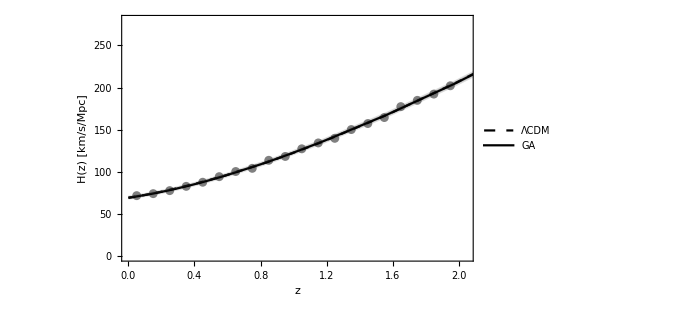

```mathematica
col=GrayLevel[0.3,0.2];
plr={{0,1.05 zmax},{0,280}};
plHzdata=Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[{H[1/(1+x),om,-1,0,1,h]/.fmin[[2]],HGA[x]+H0GA dH[x,a1,a2,0a3,0a4]ϵ0/.fminerrHtot2[[2]]}//Evaluate,{x,0,10.0 zmax},PlotStyle->{{Dashed,Black},col,Black,col},Filling->{2->{{4},col}},PlotRange->plr,Frame->True,PlotLegends->Placed[LineLegend[{{Dashed,Black},Black},{"ΛCDM","GA"}],Scaled[{0.8,0.2}]]],Frame->True,Axes->False,FrameLabel->{"z","H(z) [km/s/Mpc]"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr,ImageSize->500]
```

```mathematica
datares=Table[{data[[i,1]],data[[i,2]]-H[1/(1+data[[i,1]]),om,-1,0,1,h]/.fmin[[2]],data[[i,3]]},{i,1,Length[data]}];
```

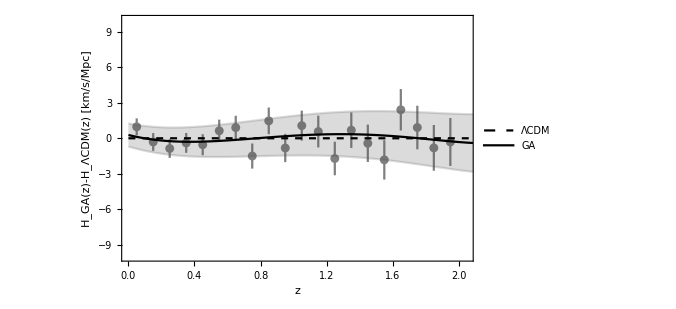

```mathematica
col=GrayLevel[0.3,0.2];
plr={{0,1.05 zmax},{-10,10}};
plHzdatares=Show[ErrorListPlot[datares,PlotRange->plr,PlotStyle->Gray],Plot[{0,HGA[x]+(H0GA dH[x,a1,a2,0a3,0a4]ϵ0/.fminerrHtot2[[2]])-(H[1/(1+x),om,-1,0,1,h]/.fmin[[2]])}//Evaluate,{x,0,10.0 zmax},PlotStyle->{{Dashed,Black},col,Black,col},Filling->{2->{{4},col}},PlotRange->plr,Frame->True,PlotLegends->Placed[LineLegend[{{Dashed,Black},Black},{"ΛCDM","GA"}],Scaled[{0.8,0.2}]]],Frame->True,Axes->False,FrameLabel->{"z","H_GA(z)-H_ΛCDM(z) [km/s/Mpc]"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr,ImageSize->500]
```

```mathematica
(* end *)
```